```mathematica
<< "~/Desktop/git/publications-of-thomas-hales/geometry/packings-of-regular-pentagons/code/pentca.m"
```

```mathematica
mm[x_]:= Mod[x,2Pi/5,-Pi/5];
elxp[xalpha_,alpha_]:= Module[{t=thetax[xalpha,alpha]},
{t[[3]],t[[1]]}];
```

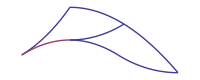

```mathematica
(* ell,theta' admissible domain *)
Clear[pp,r];
pp=ParametricPlot;
(* r [{x_,y_}]= {y,-x}; *) (* rotate*)
r[{x_,y_}]:= {x,y};
ks = Sqrt[(2kappa)^2+sigma^2];
thetapks = ArcCos[2kappa/ks];

V = pp[r[{ArcCos[(1+kappa)/t],t}],{t,1+kappa,Sqrt[(1+kappa)^2+sigma^2]}];
IV=pp[{r[{ArcCos[(1+t^2-kappa^2)/(2 t)],t}],
r[{-ArcCos[(1+t^2-kappa^2)/(2 t)],t}]},{t,ks,1+kappa}];
III = pp[r[{Pi/5 - ArcCos[2kappa/t],t}],{t,2kappa,ks}];
II= pp[r[{ArcCos[t/2],t}],{t,2kappa,2}];
Ix = pp[r[{ArcCos[2kappa/t]-Pi/5,t}],{t,ks,2}];
rotatedrange = {{2kappa,2},{-0.65,0.3}};
showElThetaXp=Show[{Ix,II,IV,III,V}, Axes->False, 
ImageSize->200,(* 300 *) PlotRange->{{-0.3,0.65},{2kappa,2}}]
```

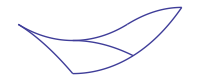

```mathematica
(* Now (ell,theta) coordinates *)
Clear[pp,r];
pp=ParametricPlot;
 (*r [{x_,y_}]= {y,-x}; *)
 (* rotate*)
r[{x_,y_}]:= {x,y};
DV = pp[r[{Pi/5+ArcCos[(kappa^2+t^2-1)/(2t kappa)],t}],{t,ks,1+kappa}];
DIV=pp[r[{th,(1+kappa)/Cos[Pi/5-th]}],{th,Pi/10,3Pi/10}];
DIII = pp[r[{th,2Cos[th-2Pi/5]}],{th,3Pi/10,2Pi/5}];
DII= pp[r[{th,2kappa/Cos[th-Pi/5]}],{th,Pi/5,2Pi/5}];
DI = pp[r[{th,2Cos[th]}],{th,Pi/10,Pi/5}];
D0 = pp[r[{th,2Cos[Pi/10]}],{th,Pi/10,3Pi/10}];
rotatedrange = {{2kappa,2},{-2Pi/5,-Pi/10}};
showElThetaZ=Show[{DI,DII,DIII,DIV,DV}, Axes->False, 
ImageSize->200,(* 300 *) PlotRange->{{Pi/10,2Pi/5},{2kappa,2}}]
```

```mathematica
Clear[r,delta,phip];
thetaHpos[lx_,thetap_]:= Module[{ly,r,h,xa,delta,phip,alpha,theta},
ly = loc[1,lx,2Pi/5-thetap];
r = loc[1,lx,thetap];
h = Sqrt[r^2 - kappa^2];
xa = h + sigma;
delta = 3Pi/10  +arc[r,2sigma,ly];
phip = ArcSin[h/r];
alpha = 6Pi/5 - phip - delta;
theta = alpha-thetap;
theta];
thetaPacute[lx_,theta_]:=
	Module[{x,phi,alphap,thetap},x = Sin[3Pi/10]/Sin[7Pi/10-theta];
phi = ArcSin[(lx-x)Sin[theta+3Pi/10]];
alphap = phi - 3Pi/10;
thetap = 2Pi/5 - alphap-theta;
thetap];
```

```mathematica
ParametricPlot3D[{lx,thp,thetaHpos[lx,thp]},
{thp,thetapks-Pi/5,0},{lx,Cos[thp]+Sqrt[Cos[thp]^2+kappa^2-1],2kappa/(Cos[thp+Pi/5])}]
```

-Graphics3D-

```mathematica
thetaHpos[Sqrt[2(1+kappa)],Pi/10]//N
```

0.314159

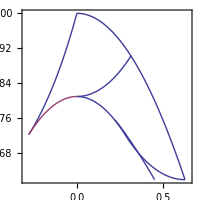

```mathematica
cp=ContourPlot[thetaHpos[t,thp]==0.9,{thp,-0.28,0.628},{t,2kappa,2},Axes->False];
Show[{cp,Ix,II,IV,III,V}, Axes->False, 
ImageSize->200,(* 300 *) PlotRange->{{-0.3,0.65},{2kappa,2}}]
```

```mathematica
thetaPacute[1+kappa,Pi/5]//N
```

0.

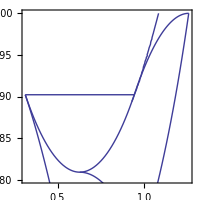

```mathematica
dp=ContourPlot[thetaPacute[t,th]==-0.3,{th,Pi/10,2Pi/5},{t,2kappa,2},Axes->False];
Show[{dp,D0,DI,DII,DIII,DIV,DV}, Axes->False, 
ImageSize->200,(* 300 *) PlotRange->{{Pi/10,2Pi/5},{1.8,2}}]
```

```mathematica
Sqrt[2(1+kappa)]//N
```

1.90211

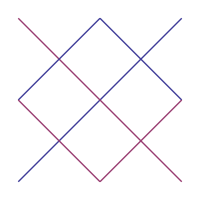

```mathematica
(* Now (theta,theta') coordinates *)
Clear[pp,r];
pp=ParametricPlot;
 (*r [{x_,y_}]= {y,-x}; *)
 (* rotate*)
r[{x_,y_}]:= {x,y};
E1 = pp[{r[{th,th}],r[{th,-th}]},{th,0,Pi/5}];
E2 = pp[{r[{th,2Pi/5-th}],r[{th,th-2Pi/5}]},{th,Pi/5,2Pi/5}];
E0 = pp[{r[{th,th-Pi/5}],r[{th,-th+Pi/5}]},{th,0,2Pi/5}];
rotatedrange = {{2kappa,2},{-2Pi/5,-Pi/10}};
showElThetaE=Show[{E0,E1,E2}, Axes->False, 
ImageSize->200,(* 300 *) PlotRange->{{0,2Pi/5},{-Pi/5,Pi/5}}]
```

```mathematica
ellz[theta_,thetap_]:= Module[{alpha,alphap,x,y},
alpha = theta+thetap;
alphap = 2Pi/5-alpha;
x = Sin[3Pi/10]/Sin[theta+3Pi/10];
y = Sin[alphap+3Pi/10]/Sin[thetap+alphap+3Pi/10];
{x,y,(x+y)}];
```

```mathematica
ellz[0.4318545,0.201379]
```

{0.824885,1.0196,1.84449}

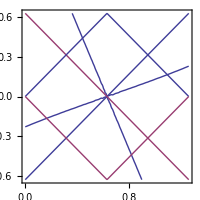

```mathematica
ep=ContourPlot[ellz[th,thp]==1.809,{th,0,2Pi/5},{thp,-Pi/5,Pi/5},Axes->False];
Show[{ep,E0,E1,E2}, Axes->False, 
ImageSize->200,(* 300 *) PlotRange->{{0,2Pi/5},{-Pi/5,Pi/5}}]
```